```mathematica
Kc b + Kc (-c)(n-1)+Kc b (n-2)//Simplify
```

(b-c) Kc (-1+n)

```mathematica
CDB=-(-c + Kc (-c) + b Kcin )/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
BDB=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
```

```mathematica
XX=(1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}
```

(-c+b (-(1-m)^2/n-m^2/(-n+d n))-c (-(1-m)^2/n-m^2/(-n+d n))) (1-Qout)+(b+b (-(1-m)^2/n-m^2/(-n+d n))+b (-2+n) (-(1-m)^2/n-m^2/(-n+d n))-c (-1+n) (-(1-m)^2/n-m^2/(-n+d n))) (Qin-Qout)

```mathematica
BH=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
CH=-(-c + Kc (-c) + b Kcin )/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

c+((b-c) (-1+d (-1+m)^2+2 m))/((-1+d) n)

```mathematica
prms={b->15,c->1,d->15,n->4}
```

{b→15,c→1,d→15,n→4}

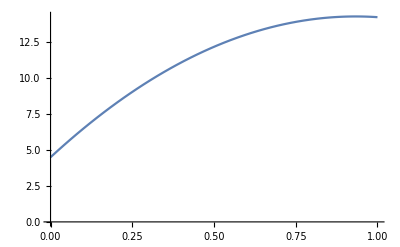

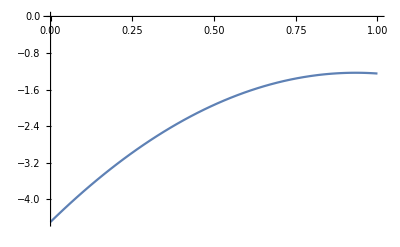

```mathematica
Plot[BH/.prms,{m,0,1},AxesOrigin->{0,0}]
Plot[-CH/.prms,{m,0,1},AxesOrigin->{0,0}]
```

```mathematica
QinM=-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QoutM=(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QinWF=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
QoutWF=(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
```

```mathematica
R2M=(Qin-Qout)/(1-Qout)/.{Qin->QinM,Qout->QoutM};
R2WF=(Qin-Qout)/(1-Qout)/.{Qin->QinWF,Qout->QoutWF};
```

```mathematica
R2M//FullSimplify
rrr=Limit[R2M,d->∞]//FullSimplify
Factor[Numerator[rrr]]
FullSimplify[Denominator[rrr]]
```

-((1+d (-1+m)) (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(-1+m) (-1+μ)

-1+m (-1+n) (-1+μ)+μ-n μ

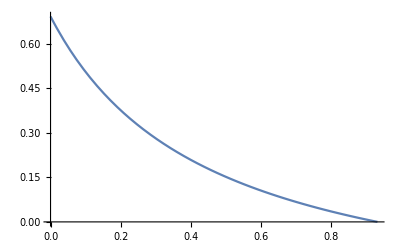

```mathematica
Plot[R2M/.prms/.μ->0.1,{m,0,(d-1)/d/.prms},AxesOrigin->{0,0}]
```

```mathematica
D[R2M,m]//FullSimplify
D[R2WF,m]//FullSimplify
Solve[%==0,m]
```

((-1+d) d n (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

(2 (-1+d)^2 d (1+d (-1+m)) n (-1+μ)^2)/(-1+d (2 (1+m (-1+n))+d (-1+(-2+m) m (-1+n)))+2 μ-2 (d (2+d (-1+m)) (-1+m) (-1+n)+n) μ+(1+d (-1+m))^2 (-1+n) μ^2)^2

{{m→(-1+d)/d}}

```mathematica
Collect[XX,{b,c},FullSimplify]
```

1/((-1+d) n)c (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+d ((-1+n) (-1+Qin)+m^2 (1+(-1+n) Qin-n Qout)+2 m (-1+Qin-n Qin+n Qout)))+(b (1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout))))/((-1+d) n)

```mathematica
Assuming[c>0,FullSimplify[(XX/.b->0)/-c/.Qout->0]]
```

-(-1+d+2 m-2 d m+d m^2+n-d n+(-1+d (-1+m)^2+2 m) (-1+n) Qin)/((-1+d) n)

```mathematica
β=Qin-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

Qin-((1-m)^2+m^2/(-1+d)) (1/n+((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
bb=Assuming[c>0,FullSimplify[(XX/.c->0)/b]]//FullSimplify
```

(1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout)))/((-1+d) n)

```mathematica
bb-β//FullSimplify
```

0

```mathematica
γ=1+-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

1+((1-m)^2+m^2/(-1+d)) (-1/n-((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
cc=Assuming[c>0,FullSimplify[(XX/.b->0)/-c]]
```

1/((-1+d) n)((-1+n) (-1+Qin)+2 m (-1+Qin-n Qin+n Qout)+d (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+m^2 (-1+Qin-n Qin+n Qout)))

```mathematica
cc-γ//FullSimplify
```

0

```mathematica
D[BH,m]//FullSimplify
Solve[%==0]

D[CH,m]//FullSimplify
Solve[%==0]
```

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

{{c→b},{m→(-1+d)/d},{n→1}}

((b-c) (2+2 d (-1+m)))/((-1+d) n)

{{c→b},{m→(-1+d)/d}}

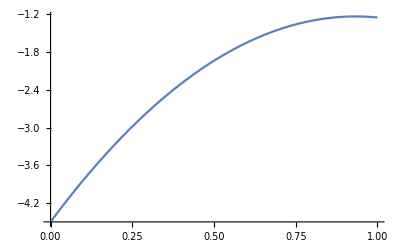

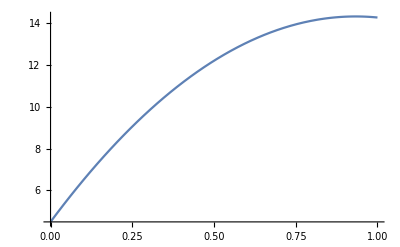

```mathematica
Plot[-CH/.{b->15,c->1,d->15,n->4},{m,0,1}]
Plot[BH/.{b->15,c->1,d->15,n->4},{m,0,1}]
```

## BD

```mathematica
XX=n d(1-Qout)(-c(μ/(n d)^2+1/(n d)(1-μ-din))+b(μ/(n d)^2+1/(n d)(-din)))+n d(b μ/(n d)^2-b din/(n d)+b/(n d (n-1))(1-μ)+(μ/(n d)^2+1/(n d)(-din))(-c))(Qin-Qout)//FullSimplify
```

1/(d (-1+n) n)(b (d n (-din (-1+n) (1+Qin-2 Qout)-(Qin-Qout) (-1+μ))+(-1+n) (1+Qin-2 Qout) μ)+c (-1+n) (-(1+Qin-2 Qout) μ+d n (-1+din (1+Qin-2 Qout)+Qout+μ-Qout μ)))

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
β=βBDD-βBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
γ=γBDD-γBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
```

(d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)/(d n)

((1+(-1+n) Qin-n Qout) μ-d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ))/(d n)

```mathematica
(β - (XX/.c->0))/b//FullSimplify
```

1/(b d n)((d n (din (-1+n) (-1+b+Qin+b Qin-n Qin-2 b Qout+n Qout)+(1+b-n) (Qin-Qout) (-1+μ)))/(-1+n)-(-1+Qin-n Qin+b (1+Qin-2 Qout)+n Qout) μ)

```mathematica
Collect[β,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

```mathematica
Collect[(XX/.c->0)/b,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+(Qin (d n (1+din-din n-μ)+(-1+n) μ))/(d (-1+n) n)+(Qout (-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ)))/(d (-1+n) n)

```mathematica
FullSimplify[(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)//Expand]
```

(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)

```mathematica
dWfo=(1-μ)(1/(n d)-1/(n d)^2)-(din/(n d)- 1/(n d)^2);
dWfin=(1-μ)(-1/(n d)^2)-(din/(n d)-1/(n d)^2);

dWself=-c dWfo+b dWfin;
dWin=b/(n-1)dWfo-c dWfin+b(n-2)/(n-1)dWfin;
```

```mathematica
X2=dWself(1-Qout)+dWin (Qin-Qout)(n-1)//FullSimplify
```

1/(d^2 n^2)(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))

```mathematica
(β - (n d X2/.c->0))/b//FullSimplify
```

((-1+b) (d n (din (1+(-1+n) Qin-n Qout)+(Qin-Qout) (-1+μ))+(-1+Qin-n Qin+n Qout) μ))/(b d n)

```mathematica
t1=Collect[β,{Qin,Qout},FullSimplify]
t2=Collect[(n d X2/.c->0)/b,{Qin,Qout},FullSimplify]
t1-t2
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

0

```mathematica
t1=Collect[γ,{Qin,Qout},FullSimplify]
t2=Collect[-(n d X2/.b->0)/c,{Qin,Qout},FullSimplify]
t1-t2
```

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

0

```mathematica
X2
```

1/(d^2 n^2)(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))

## Decomposing μ

```mathematica
EXDB=(1-μ)/μ(1-ν)ν((1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2)))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}/.{Qin->QinM,Qout->QoutM}//FullSimplify;
```

How does the competition term change with m?

```mathematica
dK=D[-((1-m)^2/n+m^2/(n d-n)),m]//FullSimplify
```

(2+2 d (-1+m))/(n-d n)

Rewrite it in human-readable form

```mathematica
(2 (d(1-m)-1))/(n(d-1))-dK//Simplify
```

0

```mathematica
Solve[dK==0,m]
dK/.m->0//FullSimplify
```

{{m→(-1+d)/d}}

2/n

The derivative is positive until mc=1-1/d, so Kc increases with m -- this means that competition decreases with m.

1 - Qout decreases with m because its derivative is negative.

```mathematica
dQo=D[1-QoutM,m]//FullSimplify
```

((-1+d) (-1+μ) μ (1+(-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Qin - Qout decreases with m

```mathematica
D[QinM-QoutM,m]//FullSimplify
```

((-1+d) (-1+μ) μ (1+(-1+d n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Let' s rewrite EXDB.
Note that Kc < 0.

```mathematica
Ks={Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
QM={Qin->QinM,Qout->QoutM};
Fact = (1-μ)/μ(1-ν)ν;
Cpri = (1-Qout)(-c );
Csec=(1-Qout)(Kc (b-c));
Bpri = (Qin-Qout)(b);
Bsec=(Qin-Qout)(n-1)(Kc (b-c));
EXDB2=Fact(Cpri+Csec+Bpri+Bsec)/.{Qin->QinM,Qout->QoutM}/.Ks//FullSimplify
```

((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Let' s separate primary and secondary effects

```mathematica
Bsec+Csec//Simplify
```

(b-c) Kc (1+(-1+n) Qin-n Qout)

```mathematica
Pr = (Qin-Qout)(b)+(1-Qout)(-c )/.Ks/.QM//FullSimplify
Sc= Kc (b-c)((n-1)Qin-n Qout+1)/.Ks/.QM//FullSimplify
EXDB3=Fact(Pr+Sc)/.Ks/.QM//FullSimplify
```

-(μ (c+c d (-1+m-m n)+b (1+d (-1+m)) (-1+μ)+c (1+d (-1+m)) (-1+n) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((b-c) (-1+d (-1+m)^2+2 m) μ)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
EXDB3-EXDB
```

0

Check how they change with m

```mathematica
DPr=D[Pr,m]//FullSimplify
DSc=D[Sc,m]//FullSimplify
```

((-1+d) (-1+μ) μ (b+b (-1+d n) μ+c (-1+μ-n μ)))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

((b-c) μ (-1+d-d m^2+3 μ+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n)) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Primary effects: constant sign with m,

```mathematica
Solve[DPr==0,m]
```

{}

```mathematica
assumpts={n>1&&d>2&&μ>0&&μ<1&&m>0&&m<1&&b>0&&c>0&&b>c}
```

{n>1&&d>2&&μ>0&&μ<1&&m>0&&m<1&&b>0&&c>0&&b>c}

```mathematica
Assuming[assumpts,Simplify[Reduce[DPr<0,b]]]
```

b+c μ+b d n μ>c+b μ+c n μ

Primary effects decrease with m.

```mathematica
mzs=Assuming[assumpts,FullSimplify[Solve[NDSc==0,m]]]
```

{{m→((-1+d) d μ (1+(-1+n) μ)-√((-1+d) d (1+μ (-4+2 d n+(5-2 n+d (1+n (-4+d n))) μ-2 (-1+d (-1+n)) (-1+n) μ^2+d (-1+n)^2 μ^3))))/(d (-1+μ) (1+d (-1+n) μ))},{m→((-1+d) d μ (1+(-1+n) μ)+√((-1+d) d (1+μ (-4+2 d n+(5-2 n+d (1+n (-4+d n))) μ-2 (-1+d (-1+n)) (-1+n) μ^2+d (-1+n)^2 μ^3))))/(d (-1+μ) (1+d (-1+n) μ))}}

The denominator is negative, so the admissible solution cannot be the second one.

```mathematica
mz=m/.mzs⟦1⟧//FullSimplify
```

((-1+d) d μ (1+(-1+n) μ)-√((-1+d) d (1+μ (-4+2 d n+(5-2 n+d (1+n (-4+d n))) μ-2 (-1+d (-1+n)) (-1+n) μ^2+d (-1+n)^2 μ^3))))/(d (-1+μ) (1+d (-1+n) μ))

```mathematica
mzs/.μ->0//FullSimplify
```

{{m→(√((-1+d) d))/d},{m→-(√((-1+d) d))/d}}

When m is small, the derivative is always positive

```mathematica
t0=NDSc/.m->0//FullSimplify
```

(b-c) μ (-1+d+(-1+d) (-3+d+d n) μ+(-2+d) (-1+d) (-1+n) μ^2)

Let' s quickly check that this is the case

```mathematica
tt=Assuming[assumpts,FullSimplify[Solve[t0==0,μ]]]
```

{{μ→0},{μ→-(-3+d (1+n)+√(1+8 n+d^2 (1+n)^2-2 d (1+5 n)))/(2 (-2+d) (-1+n))},{μ→(3-d (1+n)+√(1+8 n+d^2 (1+n)^2-2 d (1+5 n)))/(2 (-2+d) (-1+n))}}

```mathematica
Solve[(μ/.tt⟦3⟧)==0,d]
(μ/.tt⟦3⟧)/.{d->15,n->4}//N
```

{}

-0.013995

When m is small this derivative is always of the same sign for admissible (>0) values of μ.

So we have increasing then decreasing

```mathematica
tt/.{d->5,n->4}//N
```

{{μ→0.},{μ→-2.39811},{μ→-0.0463328}}

```mathematica
(√((-1+d) d))/d/.d->15//N
```

0.966092

```mathematica
Denominator[DPr]-Denominator[DSc]
```

0

Primary and secondary effects have the same denominators so we can focus just on their numerators.

```mathematica
NDPr=Numerator[DPr]//FullSimplify
NDSc=Numerator[DSc]//FullSimplify
```

(-1+d) (-1+μ) μ (b+b (-1+d n) μ+c (-1+μ-n μ))

(b-c) μ (-1+d-d m^2+3 μ+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n)) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2)

```mathematica
Assuming[assumpts,Simplify[Reduce[NDPr<0,b]]]
```

b+c μ+b d n μ>c+b μ+c n μ

```mathematica
Assuming[assumpts,Simplify[Reduce[NDSc<0,b]]]
```

$Aborted

```mathematica
EXDB-EXDB2
```

0

```mathematica
Assuming[{m>0&&m<1},FullSimplify[D[-CDB,m]]]
Solve[%==0,m]
Assuming[{m>0&&m<1},FullSimplify[D[BDB,m]]]
```

-(2 (b-c) (1+d (-1+m)))/((-1+d) n)

{{m→(-1+d)/d}}

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

```mathematica
BDB//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

```mathematica
Limit[BDB,d->∞]//FullSimplify
```

(b (1-(-2+m) m (-1+n))+c (-1+m)^2 (-1+n))/n

```mathematica
Solve[BDB==0,b]//FullSimplify
```

{{b→(c (-1+d (-1+m)^2+2 m) (-1+n))/(1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n)}}

```mathematica
EXDB0=Limit[EXDB,μ->0]//FullSimplify
Limit[%,d->∞]
```

((b-c) (2+d (-1+m))+c d n) (-1+ν) ν

(b (-1+m)+c (1-m+n)) (-1+ν) ν ∞

```mathematica
Solve[EXDB0==0,b]//FullSimplify
Limit[b/.%,d->∞]
```

{{b→c-(c d n)/(2+d (-1+m))}}

{(c (-1+m-n))/(-1+m)}

```mathematica
ΔEXDB=EXDB - Limit[EXDB,μ->0]//FullSimplify
```

(b (-2+d-d m)+c (2+d (-1+m-n))+((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))) (-1+ν) ν

```mathematica
ΔEXDB//Factor
```

-((μ (b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-2 b d m n+c d m n+b d^2 m n-b d^2 m^2 n+c d^2 m^2 n-c d^2 m n^2-b μ+c μ+2 b d μ-2 c d μ-b d^2 μ+c d^2 μ-2 b d m μ+2 c d m μ+2 b d^2 m μ-2 c d^2 m μ-b d^2 m^2 μ+c d^2 m^2 μ+2 b n μ-c n μ-3 b d n μ+c d n μ+b d^2 n μ+3 b d m n μ-2 c d m n μ-2 b d^2 m n μ+c d^2 m n μ+b d^2 m^2 n μ-c d^2 m^2 n μ+c d n^2 μ-c d^2 n^2 μ+c d^2 m n^2 μ) (-1+ν) ν)/(-m+μ-d μ+m μ+d m μ-d m n μ-μ^2+d μ^2-d m μ^2+n μ^2-d n μ^2+d m n μ^2))

```mathematica
D[EXDB0,m]
```

(b-c) d (-1+ν) ν

```mathematica
D[ΔEXDB,m]//FullSimplify
```

(-b d+c d-((-1+μ)^2 ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (1+d (-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2+((-1+μ) (b (2+d (-1+2 m-μ))+c (-2+d (1-2 m+n+μ-n μ))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))) (-1+ν) ν

```mathematica
EXBD0=EXBD/.μ->0//FullSimplify
```

EXBD

```mathematica
EXBD0
```

EXBD